# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

ia=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
icolor=reduire[clean@Import[pathResult],reduce];

Show[{ia,ib}]

(*{1,44},{1,102} arbitrary size to make the method faster *)
dim=ImageDimensions[ia];
nx=800/reduce;
ny=700/reduce;

{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,icolor}
ImageDimensions[#]&/@{ia,ib,icolor}
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45}}

## Little functions

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

```mathematica
(* Creating list of initial Values *)
rangev0=Range[-2,2,0.2];
r=Random[];
listv0=Select[RandomReal[{-2,2},{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 && Norm[#]≤2)&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0,AspectRatio->Automatic];
```

```mathematica
affiche[{p_,v_},y_]:={RainbowColor[v],Point[{p-0.5,y+0.5}]};
```

```mathematica
RainbowColor[z_]:=Blend[{Red,Orange,Yellow,Green,Cyan,Blue,Purple},z];
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
bigTest[steps_,e_,minmaxList_,dis_]:=Block[{depth, resTable,realPVTable,pos,pv,g0},(
Table[
ic=move[ia,dis];
depth=stereoDepth[listv0,ia,ic,minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[ia,g0],ImageSize->ImageDimensions[ia]*5,ImageResolution->300];

{realPVTable,g0}

,{minmax,minmaxList}]
)]
```

## Big Tests

```mathematica
e=0.001;
```

#### Full image dis=0.5, step=1

```mathematica
dis=0.5;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=0.5, step=1

```mathematica
dis=0.5;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

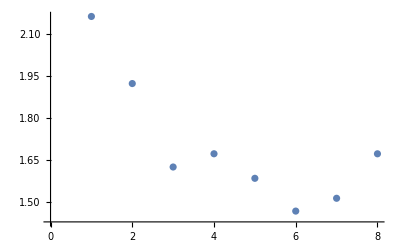

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=3;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=0.5, step=0.5

```mathematica
dis=0.5;
step=0.5;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=0.5, step=0.5

```mathematica
dis=0.5;
step=0.5;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

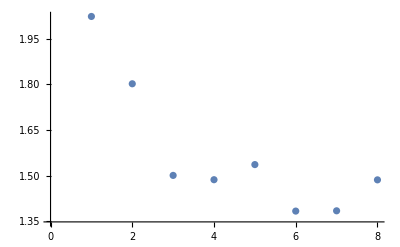

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=3;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=0.1, step=1

```mathematica
dis=0.1;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=0.1, step=1

```mathematica
dis=0.1;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

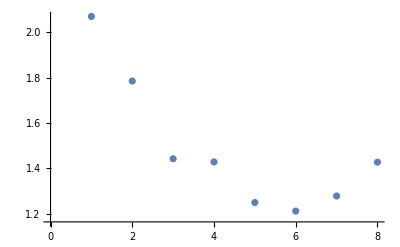

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=1.5, step=1

```mathematica
dis=1.5;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=1.5, step=1

```mathematica
dis=1.5;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

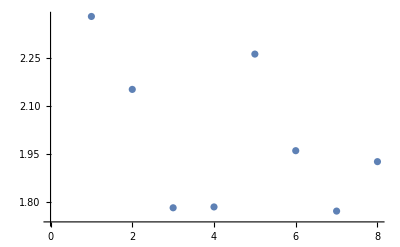

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=1.5, step=0.2

```mathematica
dis=1.5;
step=0.2;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=1.5, step=0.2

```mathematica
dis=1.5;
step=0.2;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

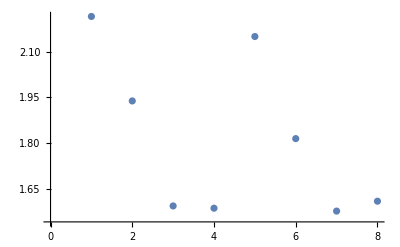

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-